```mathematica
(*Parameters*)
γ=150; 
Dil=0.5; 
R0=0.5; 
ma=0.01; mb=0.1;mc=0.05; (*Example values for m parameters*)
TI=20;
δ = 0.5;

(*Define Imax and m as before*)
Imax[T_]:=Exp[-((T-TI)^2)/γ];
m[T_]:=ma Exp[mb T]+mc;

(*Function for Req and Ce*)
ReqFunc[T_]:=m[T] R0/((1-δ) Imax[T]-m[T]);
CeFunc[T_, Req_, S_]:=Dil (S-Req)(Req + R0)/(Imax[T] Req);

(*Perform a simulation with independent draws for Req and T*)
numSimulations=10000; (*Number of simulations*)

simulationResults=Table[
Module[
{S,T, Ce, ReqVal},
(*Draw values for Req and T*)
S=RandomVariate[NormalDistribution[1.5,0.2]];
T=RandomVariate[NormalDistribution[20,5]];
(*Calculate Req and Ce based on S and T*)
ReqVal = ReqFunc[T];
Ce=CeFunc[T,ReqVal,S];
 If[Ce < 0, Ce = 0];
{S,T, Ce, ReqVal}  (*Return the values*)],{numSimulations}];
(*Calculate the 95th percentile*)
minValue=Min[simulationResults];
percentile95=Quantile[simulationResults[[All, 3]],0.95];
```

## We want to keep only values that make sense (i.e. the consumer values >= 0)

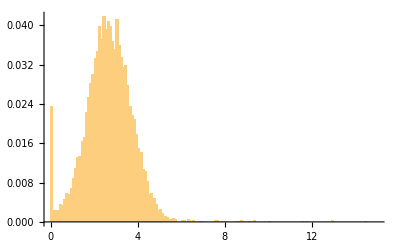

```mathematica
weirdReq = Select[simulationResults, #[[4]]> 0&]
```

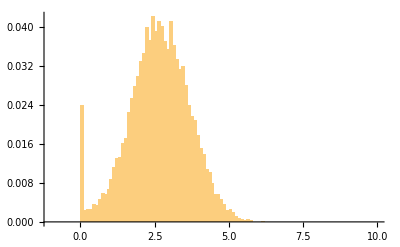

```mathematica
hist = Histogram[weirdReq[[All,3]], {-1,10,0.1}, "Probability"]

datasetName="DataSet1"; (*The name of the probability distribution dataset we're using right now*)
fileName="histogram_"<>datasetName<>".png"; (*Concatenating the file name*)

Export[fileName,hist]
```

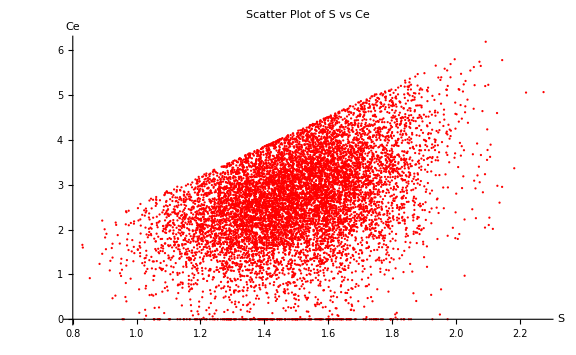

```mathematica
ListPlot[
weirdReq[[All,{1,3}]],
PlotStyle->Red,
AxesLabel->{"S","Ce"}, 
FrameLabel->{"S","Ce"},
LabelStyle->13,(*Increase the font size*)PlotLabel->Style["Scatter Plot of S vs Ce",20],(*Title of the plot*)TicksStyle->Directive[FontSize->15],(*Size of tick labels*)ImageSize->Large (*Makes the entire plot larger*)
]
```

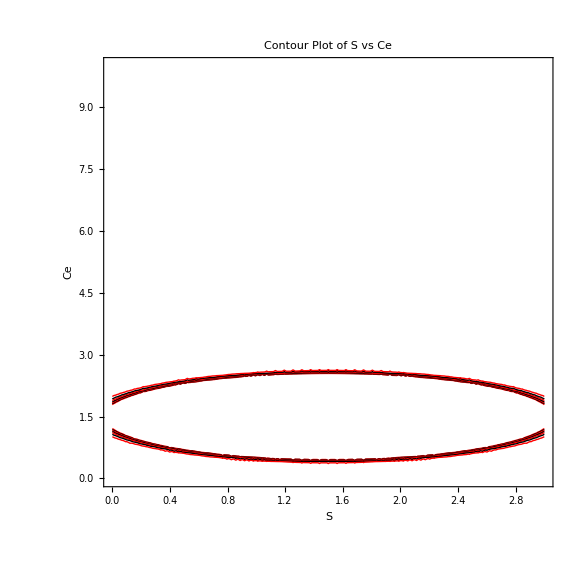

```mathematica
(*Generate the contour plot of S vs Ce with white background and density contours*)contourPlotS=ContourPlot[PDF[NormalDistribution[1.5,0.3],x]*PDF[NormalDistribution[1.5,0.2],y],{x,0,3},{y,0,10},PlotLegends->None,ContourShading->None,(*Disable color shading between contours*)ContourStyle->{Red,Thick},(*Red contour lines with thicker appearance*)PlotPoints->50,(*Increase the number of points for smoother contours*)Background->White,(*Set the background to white*)AxesLabel->{"S","Ce"},Frame->True,PlotLabel->Style["Contour Plot of S vs Ce",14],ImageSize->Large];

(*Display the contour plot*)
contourPlotS
```

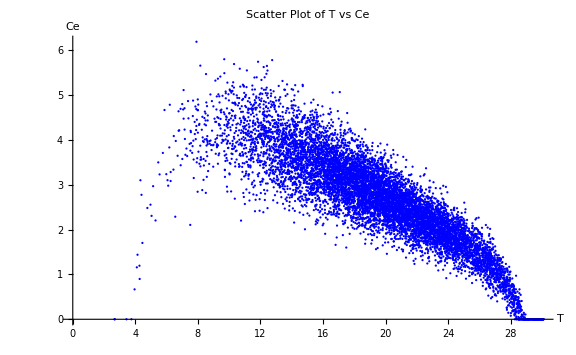

```mathematica
ListPlot[
weirdReq[[All,{2,3}]],
PlotStyle->Blue,
AxesLabel->{"T","Ce"}, 
FrameLabel->{"T","Ce"},
LabelStyle->13,(*Increase the font size*)PlotLabel->Style["Scatter Plot of T vs Ce",20],(*Title of the plot*)TicksStyle->Directive[FontSize->15],(*Size of tick labels*)ImageSize->Large (*Makes the entire plot larger*)
]
```